```mathematica
xbar[ka_,x_]:=(ka*x)/(1+(ka*x))
```

```mathematica
xrange=Table[Power[10,-ii],{ii,0,15,0.01}];
```

```mathematica
ka10pow3=ListLinePlot[Table[{Log[x],xbar[10^3,x]},{x,xrange}]];
ka10pow6=ListLinePlot[Table[{Log[x],xbar[10^6,x]},{x,xrange}],PlotStyle->Red];
ka10pow9=ListLinePlot[Table[{Log[x],xbar[10^9,x]},{x,xrange}],PlotStyle->Green];
ka10pow12=ListLinePlot[Table[{Log[x],xbar[10^12,x]},{x,xrange}],PlotStyle->Purple];
```

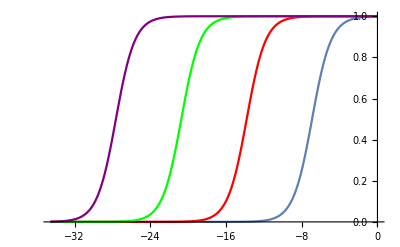

```mathematica
Show[ka10pow3,ka10pow6,ka10pow9,ka10pow12]
```

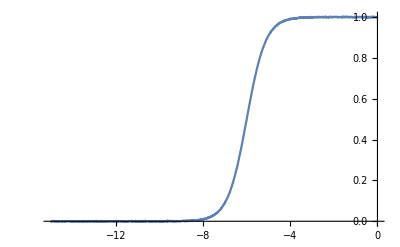

| Estimate | Standard Error | t-Statistic | P-Value
ka | 1.00017×10^6 | 368.226 | 2716.2 | 2.36788671852×10^-2771

```mathematica
(*0.1% error*)
error=RandomVariate[NormalDistribution[0,0.001],Length[xrange]];
datawitherror=error+Table[xbar[10^6,x],{x,xrange}];
data=Transpose[{Log10[xrange],datawitherror}];
ListLinePlot[data]
nlm1=NonlinearModelFit[Transpose[{xrange,datawitherror}],(ka*x)/(1+(ka*x)),ka,x];
nlm1["ParameterTable"]
```

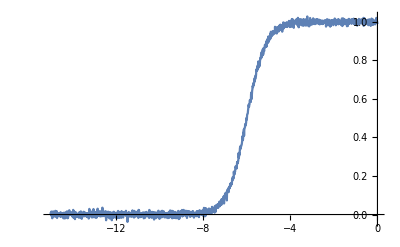

| Estimate | Standard Error | t-Statistic | P-Value
ka | 998027. | 3695.36 | 270.076 | 3.36834036899×10^-1274

```mathematica
(*1% error*)
error=RandomVariate[NormalDistribution[0,0.01],Length[xrange]];
datawitherror=error+Table[xbar[10^6,x],{x,xrange}];
data=Transpose[{Log10[xrange],datawitherror}];
ListLinePlot[data]
nlm2=NonlinearModelFit[Transpose[{xrange,datawitherror}],(ka*x)/(1+(ka*x)),ka,x];
nlm2["ParameterTable"]
```

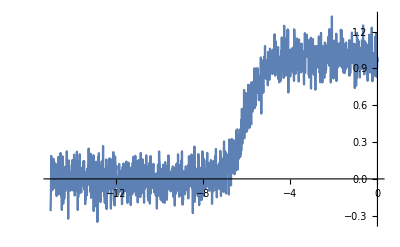

| Estimate | Standard Error | t-Statistic | P-Value
ka | 1.02793×10^6 | 37987.7 | 27.0595 | 1.17857×10^-131

```mathematica
(*10% error*)
error=RandomVariate[NormalDistribution[0,0.1],Length[xrange]];
datawitherror=error+Table[xbar[10^6,x],{x,xrange}];
data=Transpose[{Log10[xrange],datawitherror}];
ListLinePlot[data]
nlm3=NonlinearModelFit[Transpose[{xrange,datawitherror}],(ka*x)/(1+(ka*x)),ka,x];
nlm3["ParameterTable"]
```